larGrid

tempo seriale

{{1,0.0000377471},{2,0.0000216284},{3,0.000204458}}

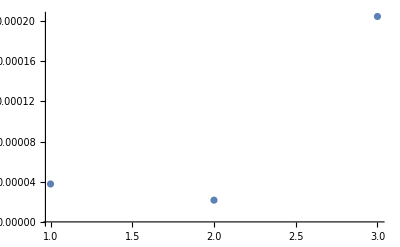

```mathematica
(*input 10,1*)
mean1= 3.7747100000000024*10^-5;
std1=0.000353252216649675;
(*input 100,1*)
mean2=2.162842*10^-5;
std2=1.4929688485915059*10^-5;
(*input 1000,1*)
mean3=0.00020445771000000002;
std3=0.0005069644058934462;
punti={{1,mean1},{2,mean2},{3,mean3}}
ListPlot[punti]
```

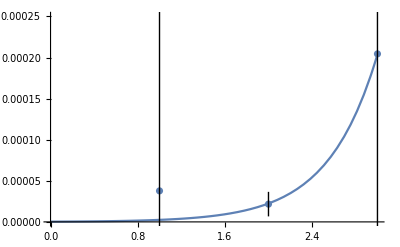

```mathematica
sfit=NonlinearModelFit[punti,a*Exp[b*x],{a,b},x,Weights->{10,100,10}];
Show[Plot[sfit["Function"][x],{x,0,3},PlotRange->{{0,0.00025}}],ListPlot[punti],Graphics[Line[{{1,mean1+std1},{1,mean1-std1}}]],Graphics[Line[{{2,mean2+std2},{2,mean2-std2}}]],Graphics[Line[{{3,mean3+std3},{3,mean3-std3}}]]]
```

tempo vettorizzato(non c’è)

tempo parallelo 4 processori

{{1,0.000892555},{2,0.000995533},{3,0.00761326}}

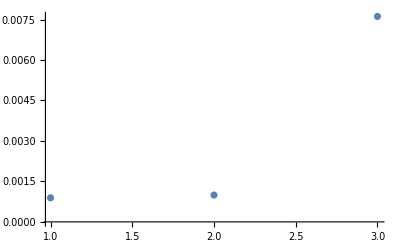

```mathematica
(*input 10,1*)
mean1= 0.0008925552699999999;
std1=0.00044143031421683406;
(*input 100,1*)
mean2=0.0009955329399999999;
std2=0.00032921670867875025;
(*input 1000,1*)
mean3=0.007613263450000001;
std3=0.019592583052351623;
punti={{1,mean1},{2,mean2},{3,mean3}}
ListPlot[punti]
```

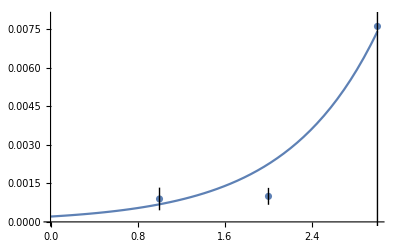

```mathematica
pfit=NonlinearModelFit[punti,a*Exp[b*x],{a,b},x,Weights->{1000,100,100}];
Show[Plot[pfit["Function"][x],{x,0,3},PlotRange->{{0,0.008}}],ListPlot[punti],Graphics[Line[{{1,mean1+std1},{1,mean1-std1}}]],Graphics[Line[{{2,mean2+std2},{2,mean2-std2}}]],Graphics[Line[{{3,mean3+std3},{3,mean3-std3}}]]]
```

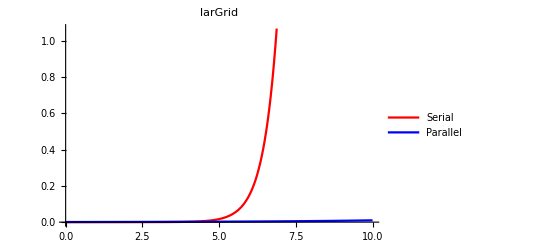

```mathematica
Show[Plot[{sfit["Function"][x],pfit["Function"][x]},{x,0,10},PlotStyle->{Red,Blue},PlotLegends->{"Serial","Parallel"},PlotLabel->"larGrid"]]
```

tesla

{{1,0.00107031},{2,0.0125818},{3,0.0120524}}

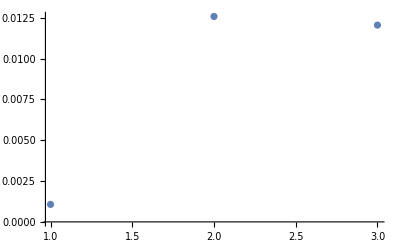

```mathematica
(*input 10,1*)
mean1= 0.0010703139000000001;
std1=0.001285278942752852;
(*input 100,1*)
mean2=0.01258177492;
std2=0.0059264938454527925;
(*input 1000,1*)
mean3=0.01205244185;
std3=0.005562518301600449;
punti={{1,mean1},{2,mean2},{3,mean3}}
ListPlot[punti]
```

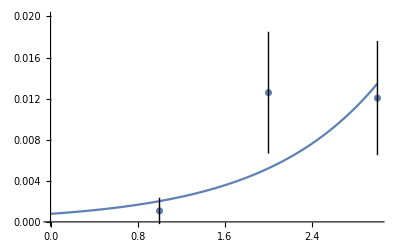

```mathematica
teslafit=NonlinearModelFit[punti,a*Exp[b*x],{a,b},x,Weights->{1000,100,100}];
Show[Plot[teslafit["Function"][x],{x,0,3},PlotRange->{0,0.02}],ListPlot[punti],Graphics[Line[{{1,mean1+std1},{1,mean1-std1}}]],Graphics[Line[{{2,mean2+std2},{2,mean2-std2}}]],Graphics[Line[{{3,mean3+std3},{3,mean3-std3}}]]]
```

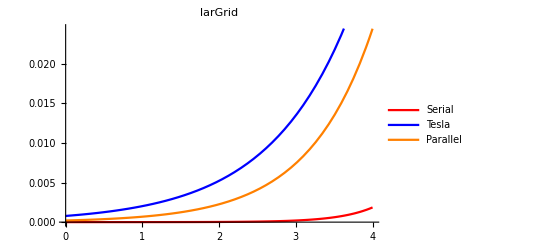

```mathematica
Plot[{sfit["Function"][x],teslafit["Function"][x],pfit["Function"][x]},{x,0,4},PlotStyle->{Red,Blue,Orange},PlotLegends->{"Serial","Tesla","Parallel"},PlotLabel->"larGrid"]
```

LarCuboidsFacets

Altre prove con altri input, solo in 2 D :
  tempo seriale

{{1,0.0000179895},{2,0.000453833},{3,0.00140335}}

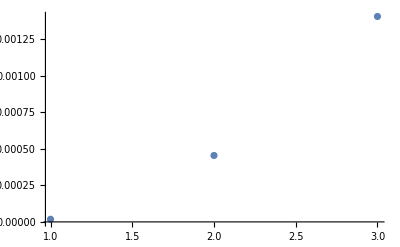

```mathematica
(*input larCuboidsFacets([0 0 1 1;0 1 0 1],[[1,2,3,4]])*)
mean1=1.7989519999999992*10^-5;
std1=9.445660453543538*10^-6;
(*input l[5,5])*)
mean2=0.00045383317000000014;
std2=0.0007042339286236128;
(*input larCuboidsFacets([10,10])*)
mean3=0.0014033473400000003;
std3=0.000569111202079442;
punti={{1,mean1},{2,mean2},{3,mean3}}
ListPlot[punti]
```

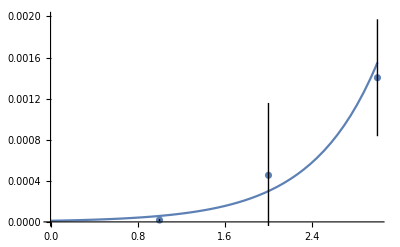

```mathematica
sfit=NonlinearModelFit[punti,a*Exp[b*x],{a,b},x,Weights->{1000,100,10}];
Show[Plot[sfit["Function"][x],{x,0,3},PlotRange->{0,0.002}],ListPlot[punti],Graphics[Line[{{1,mean1+std1},{1,mean1-std1}}]],Graphics[Line[{{2,mean2+std2},{2,mean2-std2}}]],Graphics[Line[{{3,mean3+std3},{3,mean3-std3}}]]]
```

tempo vettorizzato

{{1,0.0000238678},{2,0.00049437},{3,0.00176196}}

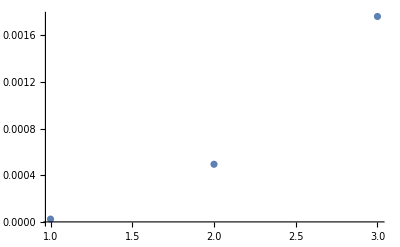

```mathematica
(*input larCuboidsFacets([0 0 1 1;0 1 0 1],[[1,2,3,4]])*)
mean1=2.386779000000001*10^-5;
std1=9.481142464397524*10^-6;
(*input [5,5])*)
mean2=0.0004943701399999999;
std2=0.0005032186692545132;
(*input [10,10])*)
mean3=0.0017619565900000005;
std3=0.0008102010629622211;
punti={{1,mean1},{2,mean2},{3,mean3}}
ListPlot[punti]
```

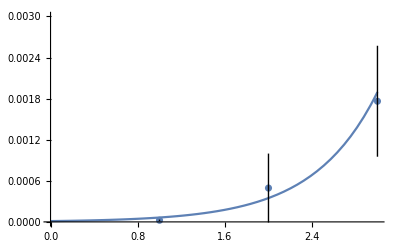

```mathematica
vfit=NonlinearModelFit[punti,a*Exp[b*x],{a,b},x,Weights->{1000,100,10}];
Show[Plot[vfit["Function"][x],{x,0,3},PlotRange->{0,0.003}],ListPlot[punti],Graphics[Line[{{1,mean1+std1},{1,mean1-std1}}]],Graphics[Line[{{2,mean2+std2},{2,mean2-std2}}]],Graphics[Line[{{3,mean3+std3},{3,mean3-std3}}]]]
```

tempo parallelo 4 processi

MAP

{{1,0.0142871},{2,0.041483},{3,0.120415}}

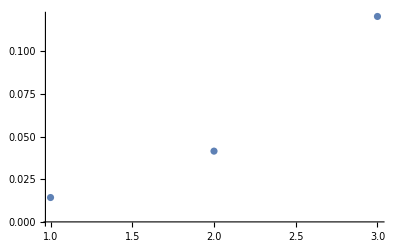

```mathematica
(*input larCuboidsFacets([0 0 1 1;0 1 0 1],[[1,2,3,4]])*)
mean1=0.014287057240000001;
std1=0.0004942629866893669;
(*input larCuboidsFacets(V,CV) larCuboids[5,5]*)
mean2=0.041483003049999995;
std2=0.002326256933510068;
(*input larCuboidsFacets([10,10])*)
mean3=0.12041468178999998;
std3=0.007527863934239976;
punti={{1,mean1},{2,mean2},{3,mean3}}
ListPlot[punti]
```

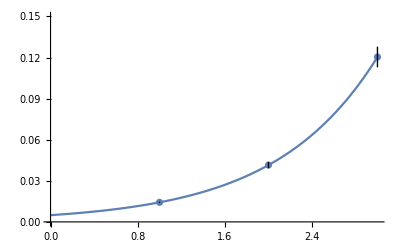

```mathematica
pmfit=NonlinearModelFit[punti,a*Exp[b*x],{a,b},x,Weights->{1000,100,10}];
Show[Plot[pmfit["Function"][x],{x,0,3},PlotRange->{0,0.15}],ListPlot[punti],Graphics[Line[{{1,mean1+std1},{1,mean1-std1}}]],Graphics[Line[{{2,mean2+std2},{2,mean2-std2}}]],Graphics[Line[{{3,mean3+std3},{3,mean3-std3}}]]]
```

LOOP

{{1,0.0189581},{2,0.0368667},{2.1,0.0518948}}

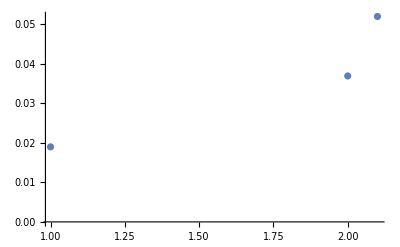

```mathematica
(*input larCuboidsFacets([0 0 1 1;0 1 0 1],[[1,2,3,4]])*)
mean1=0.018958112419999992;
std1=0.09028975630403108;
(*input larCuboidsFacets(V,CV) larCuboids[5,5]*)
mean2=0.036866681350000007;
std2=0.005771638693836112;
(*input larCuboidsFacets([6,6])*)
mean3=0.05189476432;
std3=0.00988597063185507;
punti={{1,mean1},{2,mean2},{2.1,mean3}}
ListPlot[punti]
```

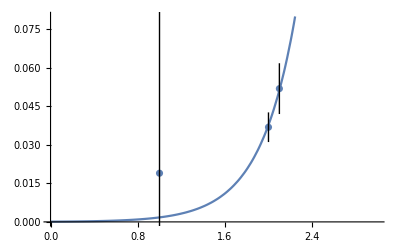

```mathematica
plfit=NonlinearModelFit[punti,a*Exp[b*x],{a,b},x,Weights->{10,100,100}];
Show[Plot[plfit["Function"][x],{x,0,3},PlotRange->{0,0.08}],ListPlot[punti],Graphics[Line[{{1,mean1+std1},{1,mean1-std1}}]],Graphics[Line[{{2,mean2+std2},{2,mean2-std2}}]],Graphics[Line[{{2.1,mean3+std3},{2.1,mean3-std3}}]]]
```

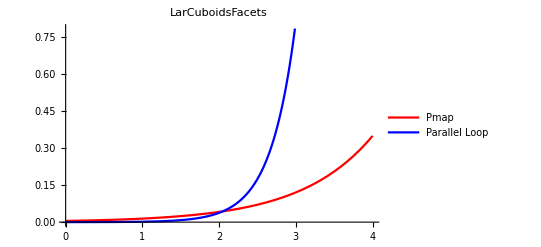

```mathematica
plot1=Show[Plot[{pmfit["Function"][x],plfit["Function"][x]},{x,0,4},PlotStyle->{Red,Blue},PlotLegends->{"Pmap","Parallel Loop"},PlotLabel->"LarCuboidsFacets"]]
```

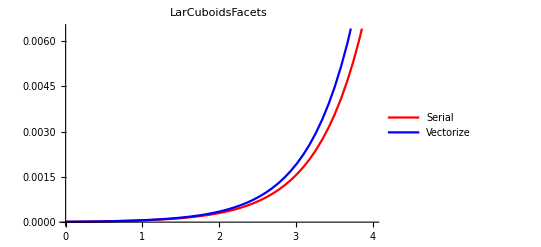

```mathematica
plot2=Show[Plot[{sfit["Function"][x],vfit["Function"][x]},{x,0,4},PlotStyle->{Red,Blue},PlotLegends->{"Serial","Vectorize"},PlotLabel->"LarCuboidsFacets"]]
```

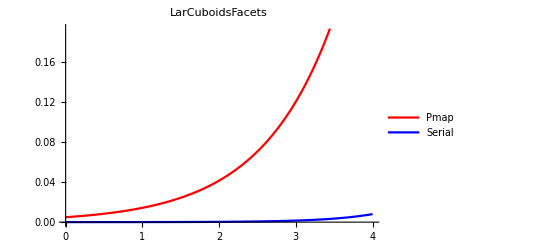

```mathematica
Show[Plot[{pmfit["Function"][x],sfit["Function"][x]},{x,0,4},PlotStyle->{Red,Blue},PlotLegends->{"Pmap","Serial"},PlotLabel->"LarCuboidsFacets"]]
```

larSimplicialStack

tempo seriale

{0.000016324,0.000586193,0.0029013}

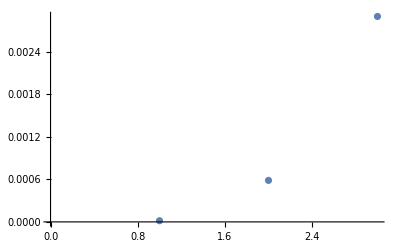

```mathematica
(*1 cella [1:4;]*)
mean1=1.6323960000000002*10^-5;
std1=4.0608037518588734*10^-7;
(*1 cella [1:8;]*)
mean2=0.00058619304;
std2=0.0004557868730846704;
(*1 cella [1:10;]*)
mean3=0.0029013027499999997;
std3=0.000943222278929349;
punti={mean1,mean2,mean3}
ListPlot[punti]
```

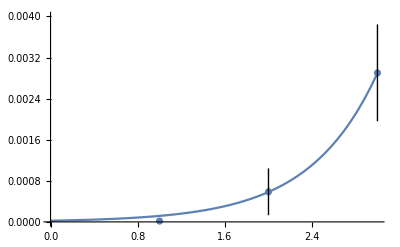

```mathematica
sfit=NonlinearModelFit[punti,a*Exp[b*x],{a,b},x,Weights->{10,100,1000}];
Show[Plot[sfit["Function"][x],{x,0,3},PlotRange->{0,0.004}],ListPlot[punti],Graphics[Line[{{1,mean1+std1},{1,mean1-std1}}]],Graphics[Line[{{2,mean2+std2},{2,mean2-std2}}]],Graphics[Line[{{3,mean3+std3},{3,mean3-std3}}]]]
```

tempo vettorizzato(non c’è)

tempo parallelo 4 processori

{0.00233166,0.0116818,0.037809}

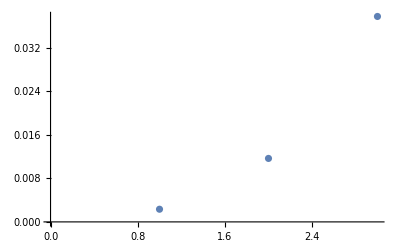

```mathematica
(*1 cella [1:4;]*)
mean1=0.00233165772;
std1=0.0005029350137672584;
(*1 cella [1:8;]*)
mean2=0.011681773740000002;
std2=0.0010725201817220048;
(*1 cella [1:10;]*)
mean3=0.03780897377;
std3=0.0027611199415448367;
punti={mean1,mean2,mean3}
ListPlot[punti]
```

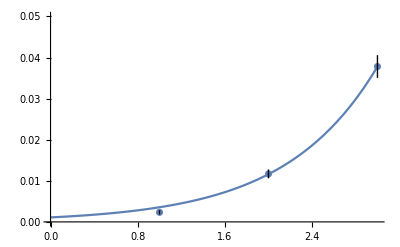

```mathematica
pfit=NonlinearModelFit[punti,a*Exp[b*x],{a,b},x,Weights->{10,100,1000}];
Show[Plot[pfit["Function"][x],{x,0,3},PlotRange->{0,0.05}],ListPlot[punti],Graphics[Line[{{1,mean1+std1},{1,mean1-std1}}]],Graphics[Line[{{2,mean2+std2},{2,mean2-std2}}]],Graphics[Line[{{3,mean3+std3},{3,mean3-std3}}]]]
```

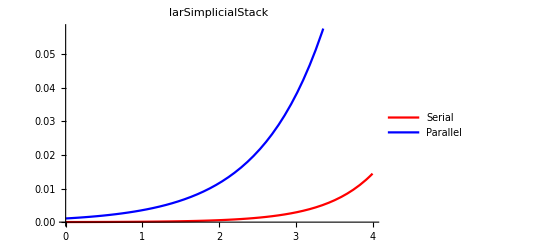

```mathematica
Show[Plot[{sfit["Function"][x],pfit["Function"][x]},{x,0,4},PlotStyle->{Red,Blue},PlotLegends->{"Serial","Parallel"},PlotLabel->"larSimplicialStack"]]
```

tesla

{{0,0},{1,2.7641×10^-7},{2,2.8636×10^-7},{3,2.5557×10^-7}}

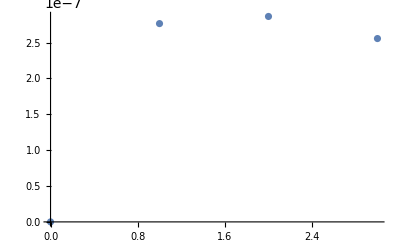

```mathematica
(*1 cella [1:4;]*)
mean1=2.7641*10^-7;
std1=2.2375645558093158*10^-7;
(*1 cella [1:8;]*)
mean2=2.8636000000000003*10^-7;
std2=1.4942269512420733*10^-7;
(*1 cella [1:10;]*)
mean3=2.5557*10^-7;
std3=1.2677947568335127*10^-7;
punti={{0,0},{1,mean1},{2,mean2},{3,mean3}}
ListPlot[punti]
```

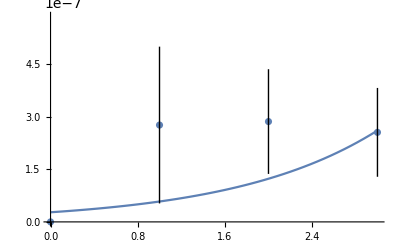

```mathematica
teslafit=NonlinearModelFit[punti,a*Exp[b*x],{a,b},x,Weights->{1000,10,100,1000}];
Show[Plot[teslafit["Function"][x],{x,0,3},PlotRange->{0,5.8636000000000003*^-7}],ListPlot[punti],Graphics[Line[{{1,mean1+std1},{1,mean1-std1}}]],Graphics[Line[{{2,mean2+std2},{2,mean2-std2}}]],Graphics[Line[{{3,mean3+std3},{3,mean3-std3}}]]]
```

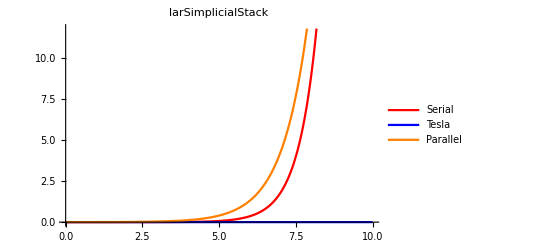

```mathematica
Plot[{sfit["Function"][x],teslafit["Function"][x],pfit["Function"][x]},{x,0,10},PlotStyle->{Red,Blue,Orange},PlotLegends->{"Serial","Tesla","Parallel"},PlotLabel->"larSimplicialStack"]
```

larGridSkeleton

tempoSeriale

{0.000114781,0.000234652,0.000610448}

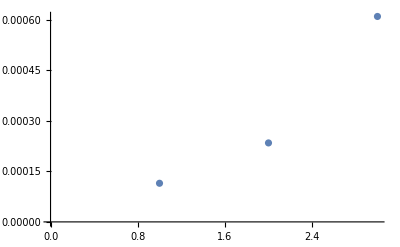

```mathematica
(*[1,1]1*)
mean1=0.00011478091999999999;
std1=0.00032823132584439493;
(*[1,1,1]1*)
mean2=0.00023465168999999995;
std2=0.00034685741003273964;
(*[1,1,1,1]1*)
mean3=0.00061044796;
std3=0.0005124251871286349;
punti={mean1,mean2,mean3}
ListPlot[punti]
```

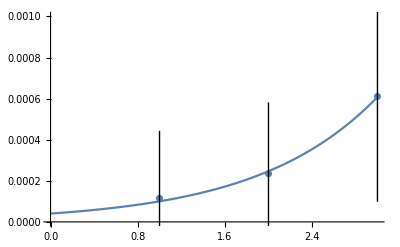

```mathematica
sfit=NonlinearModelFit[punti,a*Exp[b*x],{a,b},x];
Show[Plot[sfit["Function"][x],{x,0,3},PlotRange->{0,0.001}],ListPlot[punti],Graphics[Line[{{1,mean1+std1},{1,mean1-std1}}]],Graphics[Line[{{2,mean2+std2},{2,mean2-std2}}]],Graphics[Line[{{3,mean3+std3},{3,mean3-std3}}]]]
```

tempo vettorizzato

{0.00020658,0.000354756,0.000683698}

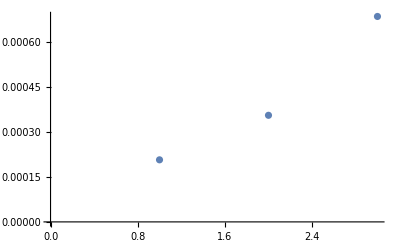

```mathematica
(*[1,1]1*)
mean1=0.00020658047;
std1=0.00039294612236299043;
(*[1,1,1]1*)
mean2=0.0003547557200000001;
std2=0.00034957102087139935;
(*[1,1,1,1]1*)
mean3=0.0006836982499999999;
std3=0.0004498851221689794;
punti={mean1,mean2,mean3}
ListPlot[punti]
```

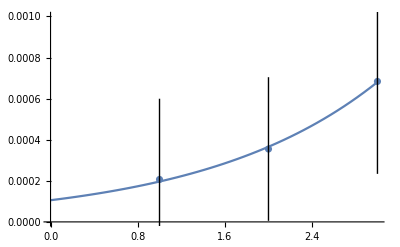

```mathematica
vfit=NonlinearModelFit[punti,a*Exp[b*x],{a,b},x];
Show[Plot[vfit["Function"][x],{x,0,3},PlotRange->{0,0.001}],ListPlot[punti],Graphics[Line[{{1,mean1+std1},{1,mean1-std1}}]],Graphics[Line[{{2,mean2+std2},{2,mean2-std2}}]],Graphics[Line[{{3,mean3+std3},{3,mean3-std3}}]]]
```

tempo parallelo 4 processori

{0.0585392,0.169555,0.436274}

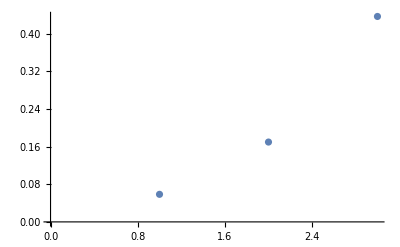

```mathematica
(*[1,1]1*)
mean1=0.05853918985000002;
std1=0.0031329461322498345;
(*[1,1,1]1*)
mean2=0.16955499371000002;
std2=0.005581195311466074;
(*[1,1,1,1]1*)
mean3=0.43627375179;
std3=0.009460042000817775;
punti={mean1,mean2,mean3}
ListPlot[punti]
```

```mathematica
{0.05853918985000002,0.16955499371000002,0.43627375179}
```

{0.0585392,0.169555,0.436274}

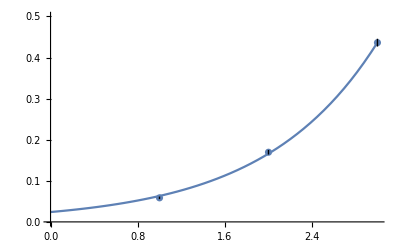

```mathematica
pfit=NonlinearModelFit[punti,a*Exp[b*x],{a,b},x];
Show[Plot[pfit["Function"][x],{x,0,3},PlotRange->{0,0.5}],ListPlot[punti],Graphics[Line[{{1,mean1+std1},{1,mean1-std1}}]],Graphics[Line[{{2,mean2+std2},{2,mean2-std2}}]],Graphics[Line[{{3,mean3+std3},{3,mean3-std3}}]]]
```

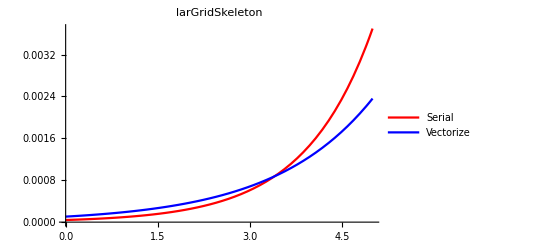

```mathematica
Show[Plot[{sfit["Function"][x],vfit["Function"][x]},{x,0,5},PlotStyle->{Red,Blue,Pink},PlotLegends->{"Serial","Vectorize"},PlotLabel->"larGridSkeleton"]]
```

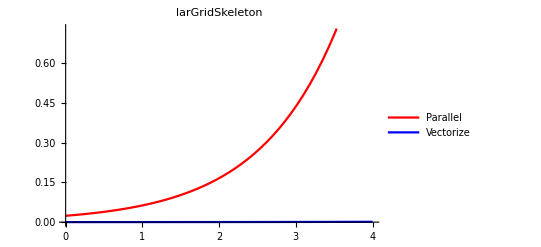

```mathematica
Show[Plot[{pfit["Function"][x],vfit["Function"][x]},{x,0,4},PlotStyle->{Red,Blue},PlotLegends->{"Parallel","Vectorize"},PlotLabel->"larGridSkeleton"]]
```

tesla

{0.0844047,0.0910177,0.205463}

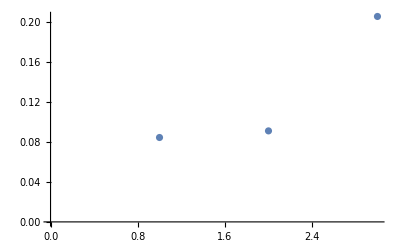

```mathematica
(*[1,1]1*)
mean1=0.08440471051000004;
std1=0.1801884761412604;
(*[1,1,1]1*)
mean2=0.09101772634000001;
std2=0.0770060240083212;
(*[1,1,1,1]1*)
mean3=0.20546323118999996;
std3=0.05151120601851886;
punti={mean1,mean2,mean3}
ListPlot[punti]
```

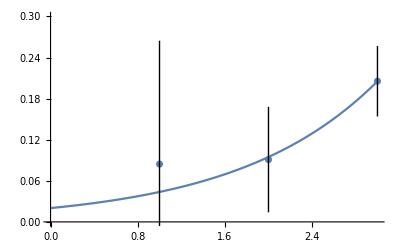

```mathematica
teslafit=NonlinearModelFit[punti,a*Exp[b*x],{a,b},x,Weights->{10,100,1000}];
Show[Plot[teslafit["Function"][x],{x,0,3},PlotRange->{0,0.3}],ListPlot[punti],Graphics[Line[{{1,mean1+std1},{1,mean1-std1}}]],Graphics[Line[{{2,mean2+std2},{2,mean2-std2}}]],Graphics[Line[{{3,mean3+std3},{3,mean3-std3}}]]]
```

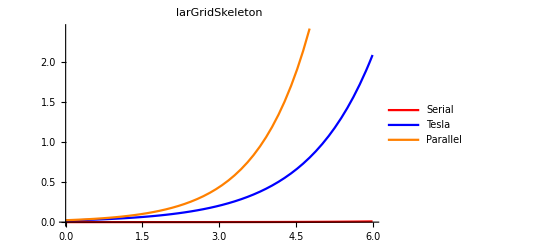

```mathematica
Plot[{sfit["Function"][x],teslafit["Function"][x],pfit["Function"][x]},{x,0,6},PlotStyle->{Red,Blue,Orange},PlotLegends->{"Serial","Tesla","Parallel"},PlotLabel->"larGridSkeleton"]
```

larCuboids

tempo seriale

{0.0000734415,0.00417774,0.0268247}

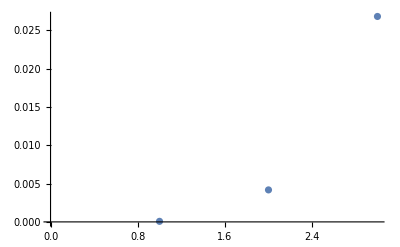

```mathematica
(*[1,1,1]*)
mean1=7.344149000000001*10^-5;
std1=1.006126360168171*10^-5;
(*[5,5,5]*)
mean2=0.00417773935;
std2=0.001188987135715223;
(*[10,10,10]*)
mean3=0.02682474011000001;
std3=0.0018179292538938493;
punti={mean1,mean2,mean3}
ListPlot[punti]
```

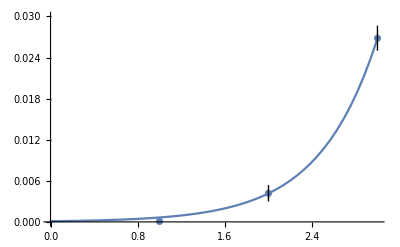

```mathematica
sfit=NonlinearModelFit[punti,a*Exp[b*x],{a,b},x,Weights->{10,100,1000}];
Show[Plot[sfit["Function"][x],{x,0,3},PlotRange->{0,0.03}],ListPlot[punti],Graphics[Line[{{1,mean1+std1},{1,mean1-std1}}]],Graphics[Line[{{2,mean2+std2},{2,mean2-std2}}]],Graphics[Line[{{3,mean3+std3},{3,mean3-std3}}]]]
```

tempo vettorizzato

{0.000177348,0.00318402,0.0228216}

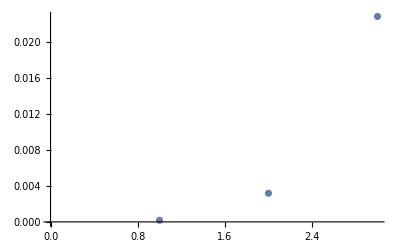

```mathematica
(*[1,1,1]*)
mean1=0.00017734750000000002;
std1=0.00038723514858690346;
(*[5,5,5]*)
mean2=0.0031840165600000004;
std2=0.0007628607076706361;
(*[10,10,10]*)
mean3=0.02282161906;
std3=0.0006082684922460883;
punti={mean1,mean2,mean3}
ListPlot[punti]
```

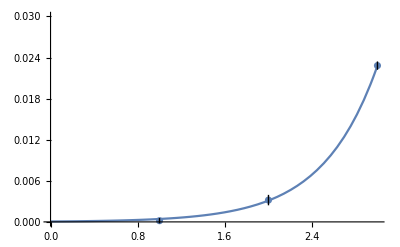

```mathematica
vfit=NonlinearModelFit[punti,a*Exp[b*x],{a,b},x];
Show[Plot[vfit["Function"][x],{x,0,3},PlotRange->{0,0.03}],ListPlot[punti],Graphics[Line[{{1,mean1+std1},{1,mean1-std1}}]],Graphics[Line[{{2,mean2+std2},{2,mean2-std2}}]],Graphics[Line[{{3,mean3+std3},{3,mean3-std3}}]]]
```

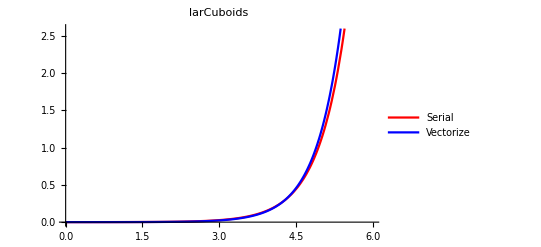

```mathematica
Plot[{sfit["Function"][x],vfit["Function"][x]},{x,0,6},PlotStyle->{Red,Blue,Pink},PlotLegends->{"Serial","Vectorize"},PlotLabel->"larCuboids"]
```

tempo parallelo 4 processori

{{1,0.0184328},{2,1.79021}}

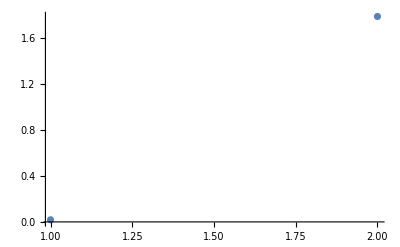

```mathematica
(*[1,1,1]*)
mean1=0.018432773830000002;
std1=0.0009873534079038848;
(*[5,5,5]*)
mean2=1.79020777473;
std2=0.01655127647344496;
(*non ce la fa*)
punti={{1,mean1},{2,mean2}}
ListPlot[punti]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

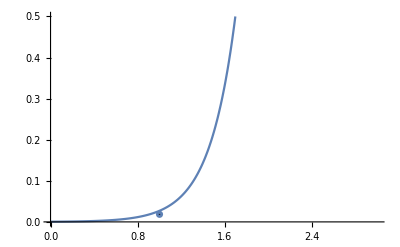

```mathematica
pfit=NonlinearModelFit[punti,a*Exp[b*x],{a,b},x,Weights->{10,100}];
Show[Plot[pfit["Function"][x],{x,0,3},PlotRange->{0,0.5}],ListPlot[punti],Graphics[Line[{{1,mean1+std1},{1,mean1-std1}}]],Graphics[Line[{{2,mean2+std2},{2,mean2-std2}}]]]
```

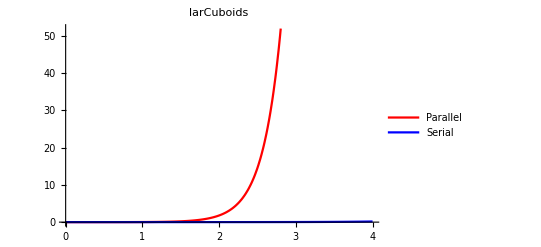

```mathematica
Show[Plot[{pfit["Function"][x],sfit["Function"][x]},{x,0,4},PlotStyle->{Red,Blue},PlotLegends->{"Parallel","Serial"},PlotLabel->"larCuboids"]]
```

tesla

{{1,0.0141769},{2,0.913046},{2.1,1.54871}}

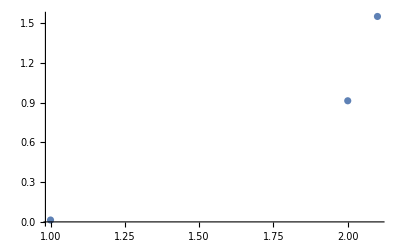

```mathematica
(*[1,1,1]*)
mean1=0.0141769283;
std1=0.005939032916280859;
(*[5,5,5]*)
mean2=0.9130463073399998;
std2=0.06806506806186609;
(*[6,6,6]*)
mean3=1.5487084196299998;
std3=0.07222423899927961;
punti={{1,mean1},{2,mean2},{2.1,mean3}}
ListPlot[punti]
```

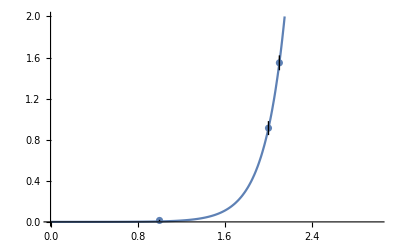

```mathematica
teslafit=NonlinearModelFit[punti,a*Exp[b*x],{a,b},x,Weights->{10,100,100}];
Show[Plot[teslafit["Function"][x],{x,0,3},PlotRange->{0,2}],ListPlot[punti],Graphics[Line[{{1,mean1+std1},{1,mean1-std1}}]],Graphics[Line[{{2,mean2+std2},{2,mean2-std2}}]],Graphics[Line[{{2.1,mean3+std3},{2.1,mean3-std3}}]]]
```

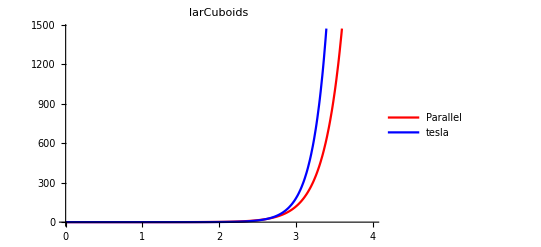

```mathematica
Show[Plot[{pfit["Function"][x],teslafit["Function"][x]},{x,0,4},PlotStyle->{Red,Blue},PlotLegends->{"Parallel","tesla"},PlotLabel->"larCuboids"]]
```

gridSkeletons

Tempo seriale

{0.000698758,0.0235491,0.179278}

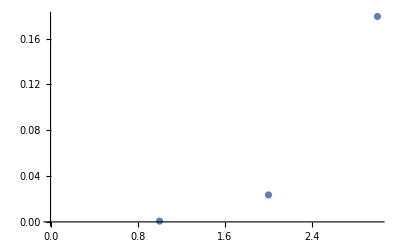

```mathematica
(*[1,1,1]*)
mean1=0.0006987578799999999;
std1=0.0005596527379882123;
(*[5,5,5]*)
mean2=0.023549119999999996;
std2=0.00329859027542757;
(*[10,10,10]*)
mean3=0.17927755159000003;
std3=0.023247172262651373;
punti={mean1,mean2,mean3}
ListPlot[punti]
```

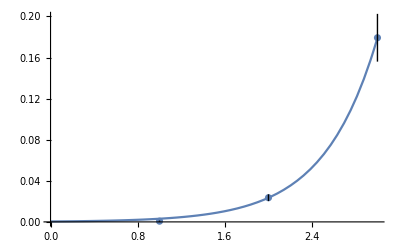

```mathematica
sfit=NonlinearModelFit[punti,a*Exp[b*x],{a,b},x,Weights->{10,100,1000}];
Show[Plot[sfit["Function"][x],{x,0,3},PlotRange->{0,0.2}],ListPlot[punti],Graphics[Line[{{1,mean1+std1},{1,mean1-std1}}]],Graphics[Line[{{2,mean2+std2},{2,mean2-std2}}]],Graphics[Line[{{3,mean3+std3},{3,mean3-std3}}]]]
```

tempo vettorizzato

{0.000854384,0.0167037,0.133761}

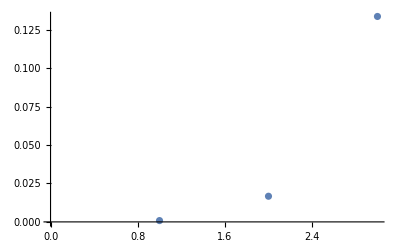

```mathematica
(*[1,1,1]*)
mean1=0.0008543836299999999;
std1=0.0006520068160661825;
(*[5,5,5]*)
mean2=0.01670374514;
std2=0.0010251223838572702;
(*[10,10,10]*)
mean3=0.13376085564;
std3=0.020574846742361576;
punti={mean1,mean2,mean3}
ListPlot[punti]
```

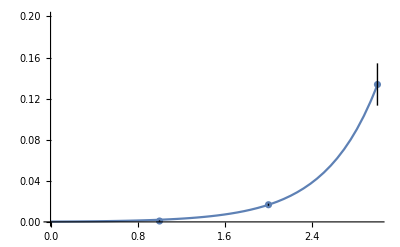

```mathematica
vfit=NonlinearModelFit[punti,a*Exp[b*x],{a,b},x,Weights->{10,100,1000}];
Show[Plot[vfit["Function"][x],{x,0,3},PlotRange->{0,0.2}],ListPlot[punti],Graphics[Line[{{1,mean1+std1},{1,mean1-std1}}]],Graphics[Line[{{2,mean2+std2},{2,mean2-std2}}]],Graphics[Line[{{3,mean3+std3},{3,mean3-std3}}]]]
```

tempo parallelo 4 processori( troppo tempo)

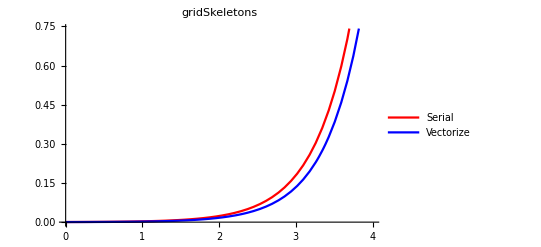

```mathematica
Show[Plot[{sfit["Function"][x],vfit["Function"][x]},{x,0,4},PlotStyle->{Red,Blue},PlotLegends->{"Serial","Vectorize"},PlotLabel->"gridSkeletons"]]
```